```mathematica
ClearAll["Global'*"]
```

## Einführung in die Computer Algebra - 2024 - Übungsblatt 5

### 3. Mini-Projekt: Datenanalyse mit Mathematica

1.  Ein Experiment misst die Energie von Photonen im Bereich zwischen 0 und 10 GeV. Die Messungen werden in ein Histogram mit 10 Bins eingetragen. Dabei umfasst Bin  den Bereich  mit  Ein Modell sagt voraus, dass der Erwartungswert in Bin  gegeben ist durch 
, wobei  und  unbekannte Parameter sind. Allerdings folgt die tatsächliche Messung einer Poisson-Verteilung, d.h. die  Anzahl beobachteter Ereignisse im Bin   ist gegeben durch PoissonDistribution[f[i]].
Schreiben Sie ein Modul, dass für gegebene Werte von  und  ein zufälliges Messergebnis erzeugt, also eine Liste mit zehn Zahlen zurückgibt, die der Anzahl beobachteter Photonen in den zehn Bins entspricht.

Hinweis: Nützliche Befehle: Module , RandomInteger, PoissonDistribution

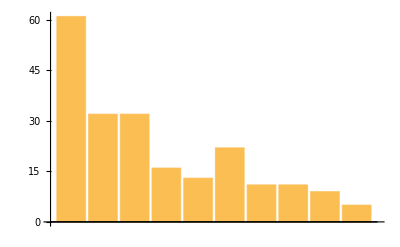

```mathematica
f[i_,a_,b_]= a/i+b;
measurements[a_,b_]:=Module[{i},data=Table[RandomInteger[PoissonDistribution[f[i,a,b]]],{i,1,10}];Return[data]
]
BarChart[measurements[50,5]]
```

2. Erzeugen Sie 1000 zufällige Messergebnisse für , . Überprüfen Sie anschließend explizit, dass der Mittelwert aller Ergebnisse im ersten Bin ungefähr durch   gegeben ist, und dass die Standardabweichung ungefähr  entspricht, wie für eine Poisson-Verteilung erwartet.

Hinweis: Nützliche Befehle: StandardDeviation

```mathematica
data2=Table[measurements[10,5],1000];
Mean[data2][[1]]//N
StandardDeviation[data2][[1]]//N
```

15.039

3.9024

```mathematica
Sqrt[f[1,10,5]]//N
```

3.87298

3. Schreiben Sie eine Likelihood-Funktion, die für gegebene Werte von  und  die Wahrscheinlichkeit eines Messergebnisses angibt. Sie können sich dabei an folgendem Beispiel orientieren.

Beispiel: Likelihood für die Parameter einer Normalverteilung basierend auf zehn Datenpunkten

```mathematica
Datenpunkte=RandomReal[NormalDistribution[4,2],10]
```

{6.16463,4.47208,4.21484,3.09346,5.88089,5.67593,0.755126,4.26518,1.2986,0.557863}

```mathematica
NormalPDF[μ_,σ_,x_]:=PDF[NormalDistribution[μ,σ],x]
```

```mathematica
LikelihoodFunk[μ_,σ_]:=Product[NormalPDF[μ,σ,Datenpunkte[[i]]],{i,1,Length[Datenpunkte]}]
```

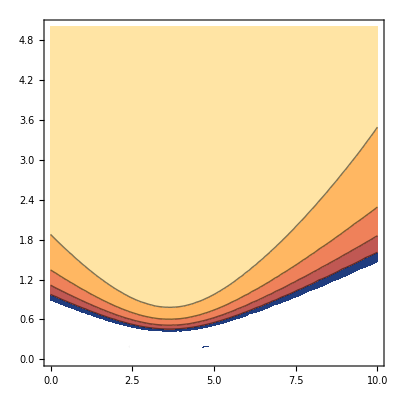

```mathematica
ContourPlot[Log[LikelihoodFunk[μ,σ]],{μ,0,10},{σ,0,5}]
```

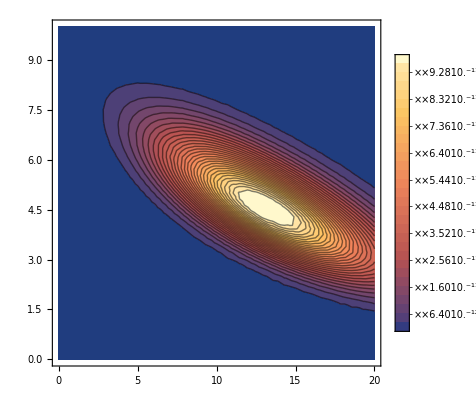

```mathematica
Clear[data]
LH[data_,a_,b_]:=Product[PDF[PoissonDistribution[f[i,a,b]],data[[i]]],{i,1,10}]
data=measurements[10,5];
ContourPlot[LH[data,a,b],{a,0,20},{b,0,10},PlotLegends->Placed[BarLegend[Automatic],Right],Contours->30,PlotRange->Full]
```

4. Schreiben Sie eine Funktion, die das Maximum der Likelihood-Funktion findet, also diejenigen Werte von a und b, die die Likelihood-Funktion maximieren. Hinweis: Es ist numerisch einfacher, den Logarithmus der Likelihood-Funktion zu benutzen. Für schnellere numerische Konvergenz dürfen Sie außerdem annehmen, dass  und  zwischen 0 und 20 liegen.

Hinweis: Nützliche Befehle: NMaximize[] .  Falls die numerische Maximierung zu langsam ist, können Sie die Präzision mittels WorkingPrecision -> ...  anpassen. WorkingPrecision gibt die Anzahl der Nachkommastellen an, die in den internen Berechnungen der Funktion benutzt werden.

```mathematica
NMaximize[{LH[data,a,b],a>0,a<20,b>0,b<20},{a,b}]
```

{5.11115×10^-13,{a→8.69562,b→8.70219}}

5. Berechnen Sie für die 1000 zufälligen Messergebnisse jeweils den Ausdruck . Dabei bezeichnet L_0 den Wert der Likelihood für  und  und L_max den maximalen Wert der Likelihood für die gefitteten Werte von a und b. Vergleichen Sie grafisch die Verteilung von q mit einer χ^2-Verteilung mit 2 Freiheitsgraden.

Hinweis: ParallelTable[ ], ChiSquareDistribution[ ]

```mathematica
result=ParallelTable[Module[{data,Lmax,L0},data=measurements[10,5];
rep=NMaximize[{Log[LH[data,a,b]],a>0,a<20,b>0,b<20},{a,b}]⟦2⟧;
L0=LH[data,10,5];
Lmax=LH[data,a,b]/. rep;
Return[-2 (Log[L0]-Log[Lmax])];],1000];
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

0.5

Plot::nonopt: Options expected (instead of PlotRange→{0,500}) beyond position 2 in Plot[binwidth 1000 PDF[ChiSquareDistribution[2],t],{t,0,Max[result]},PlotRange→{0,500}]. An option must be a rule or a list of rules.

Show::gcomb: Could not combine the graphics objects in Show[{,Plot[binwidth 1000 PDF[ChiSquareDistribution[2],t],{t,0,Max[result]},PlotRange→{0,500}],}].

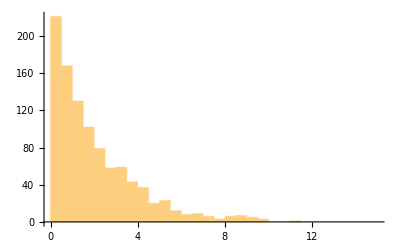
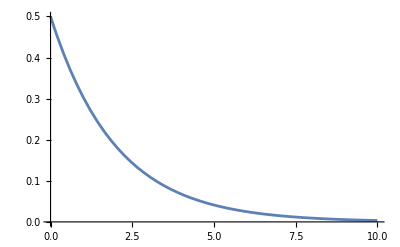
Show[{-Graphics-,Plot[binwidth 1000 PDF[ChiSquareDistribution[2],t],{t,0,Max[result]},PlotRange→{0,500}],-Graphics-}]

```mathematica
binwidth=0.5
Show[{Histogram[result,{0,15,binwidth}],Plot[binwidth 1000*PDF[ChiSquareDistribution[2],t],{t,0,Max[result]},PlotRange->{0,500}],Plot[PDF[ChiSquareDistribution[2],t],{t,0,10}]
}]
```

6.  Importieren Sie nun den Datensatz “data.dat”, der auf ILIAS zur Verfügung steht. Bestimmen Sie die Anzahl Ereignisse in jedem der zehn Bins. Berechnen Sie daraus durch Maximierung der Likelihood-Funktion die Werte von a und b.

Hinweis: Nützliche Befehle: Import[], Flatten[], BinCounts[ ]

{{0,1,2,3,4,5,6,7,8,9,10},{18,10,11,17,10,5,13,5,7,4}}

{18,10,11,17,10,5,13,5,7,4}

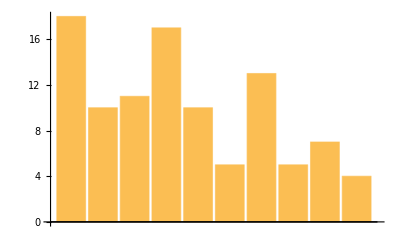

```mathematica
y =Flatten[Import["C:\\Users\\fadia\\Desktop\\Uni_codes\\mathematica\\data.dat"]];
bins = HistogramList[y,10]
count = bins[[2]]
BarChart[count]
```

```mathematica
NMaximize[{LH[count,a,b],a>0,a<20,b>0,b<20},{a,b}]
```

{6.46594×10^-13,{a→8.69562,b→8.7022}}

7.  (Optional) 
Stellen Sie grafisch den Konfidenzbereich für die Parameter a und b dar, welcher gegeben ist durch
 - 2 (log L (a, b) - log L_max) < InverseCDF[ChiSquareDistribution[2], CL] mit CL = 0.68 für 68 % Konfidenz und CL = 0.95 für 95 % Konfidenz .

Hinweis: RegionPlot, ContourPlot